```mathematica
ClearAll;
ClearAll["Global`*"];
func[x_] := 0.25*(2*x^2-x-1);
func2[x_, p0_, p1_, p2_]:=p0*D[D[func[x], x], x] + p1 *D[func[x], x] + p2*func[x];
(*coef2 = Sin[x];
coef1 = x^2;
coef0 = 1 ;*)


coef0 = 8;
coef1 = 4;
coef2 = 1;

func2[x,coef0,coef1,coef2]
FullSimplify[func2[x,coef0,coef1,coef2]]
```

8.+1. (-1+4 x)+0.25 (-1-x+2 x^2)

6.75+(3.75+0.5 x) x

```mathematica
TraditionalForm[∫(0.5 ⅇ^x x(x-1))ⅆx]
```

0.5 ⅇ^x (1. x^2-3. x+3.)

```mathematica
∫_0^x (0.5 ⅇ^v v(v-1))ⅆv
```

-1.5+ⅇ^x (1.5-1.5 x+0.5 x^2)

```mathematica
-1.5+ⅇ^x (1.5-1.5 x+0.5 x^2)
```

-1.5+ⅇ^x (1.5-1.5 x+0.5 x^2)

```mathematica
∫_0^1 (-0.5(ⅇ^-v ⅇ-ⅇ^v ⅇ^-1)v(v-1))ⅆv
```

0.0890399

```mathematica
Block[{R=1},sol=NDSolve[{8*D[D[f[t], t], t] + 4 *D[f[t], t] + f[t]=0,f[0]==-f'[0],f[1]==0},{f},t];
Column[{Plot[f[t]/.First[sol],{t,0,1}],a[0]/.First[sol]}]]
```

Set::write: Tag Plus in f[t] is Protected.

NDSolve::deqn: Equation or list of equations expected instead of 0 in the first argument 0f[0] == -SuperscriptBox[f[1] == 0.

NDSolve::dsvar: 0.0000204286 cannot be used as a variable.

ReplaceAll::reps: 0f[0] == -SuperscriptBox[f[1] == 0 is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: 0.f[0.`] == -1.` SuperscriptBox[f[1.`] == 0.` is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.0204286 cannot be used as a variable.

ReplaceAll::reps: 0f[0] == -SuperscriptBox[f[1] == 0 is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

NDSolve::dsvar: 0.0408368 cannot be used as a variable.

General::stop: Further output of NDSolve :: dsvar will be suppressed during this calculation.

NDSolve::deqn: Equation or list of equations expected instead of 0 in the first argument 0f[0] == -SuperscriptBox[f[1] == 0.

-Graphics-
a[0]/.{0,f[0]==-f'[0],f[1]==0}

```mathematica
nsol1=NDSolve[{y''[t]+y[t]/4==8,y[0]==0,y[10]==0},y,{t,0,10}]
Plot[First[y[t]/.nsol1],{t,0,10}]
```

{{y→InterpolatingFunction[{{0., 10.}}, <>]}}

{{y→InterpolatingFunction[{{0., 1.}}, <>]}}

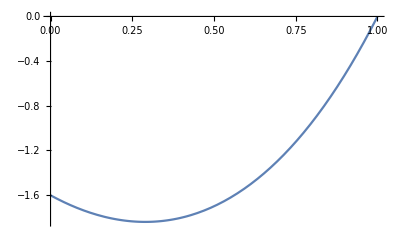

{-1.60612}

```mathematica
nsol1=NDSolve[{y''[t]-y[t]==6.75+(3.75+0.5 *t)* t,y'[0]-y[0]==0,y[1]==0},y,{t,0,1}]
Plot[First[y[t]/.nsol1],{t,0,1}]
y[0]/.nsol1
```

```mathematica
Evaluate(nsol1[0])
```

Evaluate {{y→InterpolatingFunction[{{0., 10.}}, <>]}}[0]